```mathematica
Subscript[m, 0]=0.053
Subscript[h, 0]=0.596
Subscript[n, 0]=0.318
H=0.001
R=34.5
a=0.0238
r=R/(Pi*a^2)
Subscript[c, 0]=1
c=2*Pi*a*Subscript[c, 0]
t = Min[(H^2*c*r)/5,0.01]
Gna=120;
Gk=36;
Gl=0.3;
Vna=115;
Vk=-12;
Vl=10.5995;
SolveNeuron[lMax_,TMax_]:=(
(*lMax - length of the neuron*)
(*TMax - Time*)
col = Ceiling[lMax/H];
row=Ceiling[TMax/t];
Print[row," ",col];
VV=Table[0,{row},{col}];(*l-rows T-cols*)
Do[
VV[[1,q]]=500,
{q,1,10}
];
Print["Done"];
mm=Table[Subscript[m, 0],{row},{col}];
nn=Table[Subscript[n, 0],{row},{col}];
hh=Table[Subscript[h, 0],{row},{col}];
Do[
Do[
VV[[j+1,i]]=(VV[[j,i+1]]-2*VV[[j,i]]+VV[[j,i-1]])/H^2*t/(r*c)-1/c(Gna*mm[[j,i]]^3 hh[[j,i]]*(VV[[j,i]]-Vna)+Gk*nn[[j,i]]^4(VV[[j,i]]-Vk)+Gl(VV[[j,i]]-Vl))*2*Pi*a*t+VV[[j,i]];,
{i,2,col-1}
];
Do[
mm[[j+1,u]]=((0.1 (25-VV[[j,u]]))/(ⅇ^((25-VV[[j,u]])/10)-1)(1-mm[[j,u]])-4 ⅇ^(-VV[[j,u]]/18)*mm[[j,u]])*t+mm[[j,u]];
hh[[j+1,u]]=(0.07 ⅇ^(-VV[[j,u]]/20)(1-hh[[j,u]])-hh[[j,u]]/(ⅇ^((30-VV[[j,u]])/10)+1))*t+hh[[j,u]];
nn[[j+1,u]]=((0.01 (10-VV[[j,u]]))/(ⅇ^((10-VV[[j,u]])/10)-1)(1-nn[[j,u]])-0.125 ⅇ^(-VV[[j,u]]/80)*nn[[j,u]])*t+nn[[j,u]],
{u,1,col}
],
{j,1,row-1}
];
w=Table[{q,VV[[50,q]]},{q,1,col}];
ListLinePlot[w,PlotRange->All]
)
SolveNeuron[2.5,5]
```

0.053

0.596

0.318

0.001

34.5

0.0238

19387.2

1

0.14954

0.000579832

8624 2500

Done

$Aborted

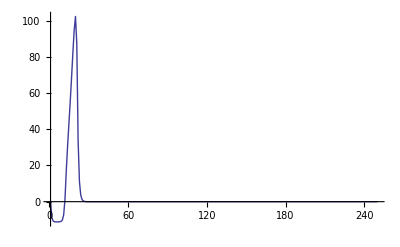

```mathematica
w=Table[{q,VV[[300,q]]},{q,1,col}];
ListLinePlot[w,PlotRange->All]
```